## Definitions

```mathematica
x = 3
```

3

```mathematica
{x, 3 x + 5}
```

{3,14}

```mathematica
Clear[x]
```

```mathematica
rand1 = RandomReal[]
```

0.628507

```mathematica
rand2 := RandomReal[]
```

```mathematica
rand2
```

0.926312

```mathematica
rand2
```

0.913018

```mathematica
?rand1
```

```mathematica
?rand2
```

```mathematica
Table[rand1,{3}]
```

{0.628507,0.628507,0.628507}

```mathematica
Table[rand2,{3}]
```

{0.950472,0.0437908,0.201797}

```mathematica
Clear[rand1, rand2, f, x]
```

```mathematica
g[n_]=Table[i^2,{i,1,n}]
```

Table::iterb: Iterator {i,1,n} does not have appropriate bounds.

Table[i^2,{i,1,n}]

```mathematica
g2[n_]:=Table[i^2,{i,1,n}]
```

```mathematica
g2[5]
```

{1,4,9,16,25}

```mathematica
Clear[g, g2]
```

```mathematica
f[x_]:=x Sin[x]
```

```mathematica
f[3]//N
```

0.42336

## Procedural Programming

```mathematica
f[x_]:=If[x>Pi,
Print[x," is larger than Pi"],
Print[x," is not larger than Pi"]]
```

```mathematica
f[E]
```

ⅇ is not larger than Pi

```mathematica
NumberQ[E]
```

False

```mathematica
Positive[E]
```

True

```mathematica
n=10;
result = 0;
Do[result = result + k,{k,1, n}];
result
```

55

```mathematica
f[n_]:=(
result = 0;
Do[result = result + k,{k,1, n}];
result
)
```

```mathematica
f[10]
```

55

```mathematica
Clear[f,n,result]
```

```mathematica
value[p_]:=p(1 + .05/12)
```

```mathematica
value[1000]
```

1004.17

```mathematica
value[value[1000]]
```

1008.35

```mathematica
Nest[value,1000,3]
```

1012.55

```mathematica
NestList[value, 1000, 12]
```

{1000,1004.17,1008.35,1012.55,1016.77,1021.01,1025.26,1029.53,1033.82,1038.13,1042.46,1046.8,1051.16}

```mathematica
Map[f,g[a,b,c]]
```

g[f[a],f[b],f[c]]

```mathematica
FullForm[a+b+c]
```

Plus[a,b,c]

```mathematica
Map[f, a+b+c]
```

f[a]+f[b]+f[c]

```mathematica
FullForm[Map]
```

Map

```mathematica
a+b+c//FullForm
```

Plus[a,b,c]

```mathematica
AtomQ[abc]
```

True

```mathematica
Head[17]
```

Integer

```mathematica
17//FullForm
```

17

```mathematica
Head["Hello"]
```

String

```mathematica
f[a,b,c]
```

f[a,b,c]

```mathematica
f[a,b,c]//FullForm
```

f[a,b,c]

```mathematica
mat={{a,b},{d,e},{g,h}}
```

{{a,b},{d,e},{g,h}}

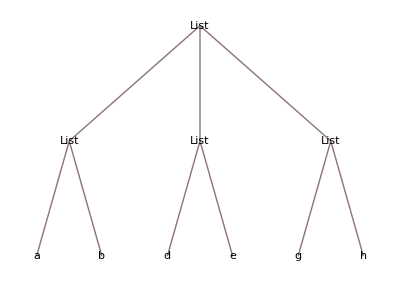

```mathematica
TreeForm[mat]
```

```mathematica
Head[mat]
```

List

```mathematica
Length[mat]
```

3

```mathematica
Part[mat,2]
```

{d,e}

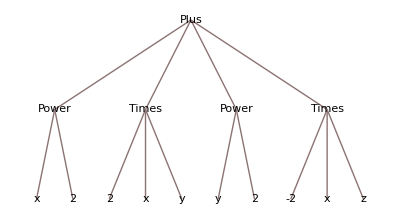

```mathematica
TreeForm[poly=x^2+2x y+y^2-2 x z]
```

```mathematica
Apply[Times,{a,b,c,d,e}]
```

a b c d e

```mathematica
Apply[Times,Range[10]]
```

3628800

```mathematica
Apply[Plus,Range[10]]
```

55

```mathematica
Total[Range[10]]
```

55

```mathematica
mat={{3,9,1},{2,7,8},{5,3,1}}
```

{{3,9,1},{2,7,8},{5,3,1}}

```mathematica
MatrixForm[mat]
```

(3 | 9 | 1
2 | 7 | 8
5 | 3 | 1)

```mathematica
Map[Max,mat]
```

{9,8,5}

```mathematica
Map[max,mat]
```

{max[{3,9,1}],max[{2,7,8}],max[{5,3,1}]}

## Programming with Rules

```mathematica
MatrixForm[mat/. 1->0]
```

(3 | 9 | 0
2 | 7 | 8
5 | 3 | 0)

```mathematica
x=5
```

5

```mathematica
2 x + x y
```

10+5 y

```mathematica
Clear[x]
```

```mathematica
ReplaceAll[2 x + x y, x->500]
```

1000+500 y

```mathematica
2 x + x y /. x-> 500
```

1000+500 y

```mathematica
SeedRandom[245];
mat=RandomInteger[{0,10},{4,4}]//MatrixForm
```

(5 | 1 | 6 | 0
3 | 1 | 2 | 7
9 | 1 | 3 | 7
1 | 8 | 0 | 5)

```mathematica
mat/.{5->500,3->300}
```

(500 | 1 | 6 | 0
300 | 1 | 2 | 7
9 | 1 | 300 | 7
1 | 8 | 0 | 500)

```mathematica
StringReplace["the cat in the hat","t"->"T"]
```

The caT in The haT

```mathematica
Clear[mat]
```